### Code used to generate the figures of manuscript “Off-fault damage controls near-surface rupture behaviour in soft sediments” (reference number: NCOMMS-24-75893). Nicola De Paola, Rachael J. Bullock, Robert E. Holdsworth, Shmuel Marco, and Stefan Nielsen. Under review in Nature Communications as of Nov. 26, 2024.

Stress intensity k0 for inhomogeneous stress (two fault segments case, use Fossum and Freund expression and integrate by parts):

```mathematica
K0a=Assuming[{L>Lr},(√π)/2 Integrate[τ1/(√(L-x)),{x,0,L1}]]+Assuming[{L>Lr},(√π)/2 Integrate[τ2/(√(L-x)),{x,L1,L}]]
```

-(-√L+√(L-L1)) √π τ1+√(L-L1) √π τ2

re-arrange to get

```mathematica
K0=√(π L)τ1(1-(1-τ2/τ1)√(1-L1/L))
```

√L √π τ1 (1-√(1-L1/L) (1-τ2/τ1))

if τ2=0 then  K0a = √(π L)τ1(1-√(1-L1/L))

for zero stress on the second segment:

```mathematica
K0a/.τ1->0
```

√(L-L1) √π τ2

get G0 (static energy flow) from K0 for plane strain

```mathematica
G0=Re[K0]^2/μ(1-ν)/2
```

(π (1-ν) Re[√L τ1 (1-√(1-L1/L) (1-τ2/τ1))]^2)/(2 μ)

#### deep (2700 m)

1.66×10^6J/m2 |1.06×10^6J/m2 |160000.J/m2 |7300---1400 m

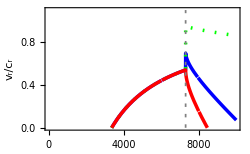

```mathematica
maxL= 10 10^3; shallo=2700;
params:={cr->1,μ->20 10^9,ν->.3,τ1->3 10^6};
(* Egcal is dissipation. 
Root value is 1.66 MJ/m2. 
Superfical value is less, with 3 different scenarios: E0, E1 oe E2  *)
Egcal[L_,L1_,add_]= 1.66 10^6+  UnitStep[L-L1] *add/.params;
(* vrcal is the rupture velocity.
vrcal is obtained from equation (2) in https://doi.org/10.1038/s41467-024-47970-6
also in equation (2) of https://doi.org/10.48550/arXiv.2411.00544 *)
vrcal=cr(1-(Egcal[ L,L1,add]/G0))/.params;
E0=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->0}/.params;
E1=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->-.6 10^6}/.params;
E2=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->-1.5 10^6}/.params;
Print[E0,"J/m2 |",E1,"J/m2 |",E2,"J/m2 |",maxL-shallo,"--",10^4-maxL-1400," m"];
plo2=Show[Plot[{
vrcal/.{L1->maxL-shallo,τ2->0,add->-.6 10^6}/.params,
vrcal/.{L1->maxL-shallo,τ2->0,add->-1.5 10^6}/.params,vrcal/.{L1->maxL-shallo,τ2->0,add->0}/.params},
{L,0,maxL},
PlotRange->{{0,maxL},{0,1.1}},
Frame->True,
PlotStyle->{{Thickness[.01],Dashing[{1,0}],Blue},{Thickness[.01],Dashing[{.005,0.03}],Green},{Thickness[.01],Dashing[{1,0}],Red}},
(*FrameTicks->{{Automatic,None},
{ {{0,10},{2000,8},{4000,6}, {6000,4}, {8000,2},{10000,0}},None}},*)
FrameLabel->{"downdip position L-x (km)","v_r/c_r",None,"surface"},
ImageSize->250],
ListLinePlot[{{maxL-shallo,0},{maxL-shallo, 1.1}},PlotStyle->{{Thickness[.005],Dashing[{.01,0.02}],Gray}}]]
```

#### Intermediate (1400 m)

1.66×10^6J/m2 |1.06×10^6J/m2 |160000.J/m2 |8600---1400 m

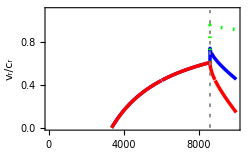

```mathematica
maxL= 10 10^3; shallo=1400;
params:={cr->1,μ->20 10^9,ν->.3,τ1->3 10^6};
Egcal[L_,L1_,add_]= 1.66 10^6+  UnitStep[L-L1] *add/.params;
vrcal=cr(1-(Egcal[ L,L1,add]/G0))/.params;
E0=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->0}/.params;
E1=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->-.6 10^6}/.params;
E2=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->-1.5 10^6}/.params;
Print[E0,"J/m2 |",E1,"J/m2 |",E2,"J/m2 |",maxL-shallo,"--",10^4-maxL-1400," m"];
plo2=Show[Plot[{
vrcal/.{L1->maxL-shallo,τ2->0,add->-.6 10^6}/.params,
vrcal/.{L1->maxL-shallo,τ2->0,add->-1.5 10^6}/.params,vrcal/.{L1->maxL-shallo,τ2->0,add->0}/.params},
{L,0,maxL},
PlotRange->{{0,maxL},{0,1.1}},
Frame->True,
PlotStyle->{{Thickness[.01],Dashing[{1,0}],Blue},{Thickness[.01],Dashing[{.005,0.03}],Green},{Thickness[.01],Dashing[{1,0}],Red}},
(*FrameTicks->{{Automatic,None},
{ {{0,10},{2000,8},{4000,6}, {6000,4}, {8000,2},{10000,0}},None}},*)
FrameLabel->{"downdip position L-x (km)","v_r/c_r",None,"surface"},
ImageSize->250],
ListLinePlot[{{maxL-shallo,0},{maxL-shallo, 1.1}},PlotStyle->{{Thickness[.005],Dashing[{.01,0.02}],Gray}}]]
```

#### Shallow (300 m, i.e. Lisan formation thickness)

1.66×10^6J/m2 |1.06×10^6J/m2 |160000.J/m2 |9700---1400 m |nuc dep:6.6

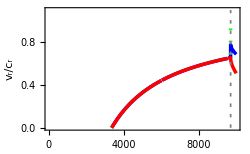

```mathematica
maxL= 10 10^3; shallo=300;
params:={cr->1,μ->20 10^9,ν->.3,τ1->3 10^6};
Egcal[L_,L1_,add_]= 1.66 10^6+  UnitStep[L-L1] *add/.params;
vrcal=cr(1-(Egcal[ L,L1,add]/G0))/.params;
E0=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->0}/.params;
E1=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->-.6 10^6}/.params;
E2=Egcal[maxL,maxL,add]/.{L1->maxL-shallo,τ2->0,add->-1.5 10^6}/.params;
Print[E0,"J/m2 |",E1,"J/m2 |",E2,"J/m2 |",maxL-shallo,"--",10^4-maxL-1400," m |","nuc dep:",10-3.4];
plo2=Show[Plot[{
vrcal/.{L1->maxL-shallo,τ2->0,add->-.6 10^6}/.params,
vrcal/.{L1->maxL-shallo,τ2->0,add->-1.5 10^6}/.params,vrcal/.{L1->maxL-shallo,τ2->0,add->0}/.params},
{L,0,maxL},
PlotRange->{{0,maxL},{0,1.1}},
Frame->True,
PlotStyle->{{Thickness[.01],Dashing[{1,0}],Blue},{Thickness[.01],Dashing[{.005,0.03}],Green},{Thickness[.01],Dashing[{1,0}],Red}},
(*FrameTicks->{{Automatic,None},
{ {{0,10},{2000,8},{4000,6}, {6000,4}, {8000,2},{10000,0}},None}},*)
FrameLabel->{"downdip position L-x (km)","v_r/c_r",None,"surface"},
ImageSize->250],
ListLinePlot[{{maxL-shallo,0},{maxL-shallo, 1.1}},PlotStyle->{{Thickness[.005],Dashing[{.01,0.02}],Gray}}]]
```